# Katz mass: Is there a solution (XYZT)?

## The idea is to figure out the mass formula (which I do in the Jupyter doc), then put this into the Einstein Field Equations, which spit out a T tensor, and that ‘T’ represents the gravitational energy density (which should NOT be the Katz formula exactly, as we now ascribe mass to the gravitational field).

So I take an isotropic Schwarzchild, and instead of mass being a constant, I lower the mass as one approaches the horizon, we assume that the energy is given to the Gravitational Field energy  - like Katz.

## The mass formula as a function of radius was found by tom

Here is the formula from Katz - in isotropic coords, the gravitational field energy outside isotropic r is 
m^2/2r - BUT as we move in in radius, the available mass left to make the central bit drops, and thus we are left with.  So in Dec 2024, I calculated that the mass inside isotropic r decreases as  M = m - m/(1 + 2r/m) See the Jupyter doc.  I also assume Birchoff’s theorem...I numerically obtained a solution to the integral equation for Brown-York Katz gravitational energy density... Isotropic... (likely there is an analytic version).

So use this as our mass formula

```mathematica
R := Sqrt[x^2 + y^2 + z^2]
```

```mathematica
M := m - m /(1 + 2 R/m)
```

Use the isotropic metric, but use ‘big M’ - mass as a function of r as above...

And sub it into the isotropic metric...

-Graphics-

```mathematica
pointMassMetricXYZT = ResourceFunction["MetricTensor"][{{(-(M - 2 R)^2)/(M + 2 R)^2,0,0,0},{0,(1 + M/(2 R))^4,0,0},{0,0,(1 + M/(2 R))^4,0},{0,0,0, (1 + M/(2 R))^4}}, {t, x,y, z}]
```

MetricTensor[…]

The metric looks quite neat and small, actually...

```mathematica
pointMassMetricXYZT["ReducedMatrixRepresentation"] // MatrixForm
```

(-(x^2+y^2+z^2)/((m+√(x^2+y^2+z^2))^2) | 0 | 0 | 0
0 | (16 (m+√(x^2+y^2+z^2))^4)/((m+2 √(x^2+y^2+z^2))^4) | 0 | 0
0 | 0 | (16 (m+√(x^2+y^2+z^2))^4)/((m+2 √(x^2+y^2+z^2))^4) | 0
0 | 0 | 0 | (16 (m+√(x^2+y^2+z^2))^4)/((m+2 √(x^2+y^2+z^2))^4))

```mathematica
pointMassMetricXYZT["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,MetricSingularities,Determinant,ReducedDeterminant,Trace,ReducedTrace,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,MetricTensor,InverseMetricTensor,LineElement,ReducedLineElement,VolumeForm,ReducedVolumeForm,TimelikeQ,LightlikeQ,SpacelikeQ,LengthPureFunction,AnglePureFunction,Properties}

```mathematica
pointMassMetricXYZT["MetricSingularities"]
```

{{x→0,y→0,z→0},{z→-√(m^2-x^2-y^2)},{z→√(m^2-x^2-y^2)},{z→-1/2 √(m^2-4 x^2-4 y^2)},{z→1/2 √(m^2-4 x^2-4 y^2)}}

```mathematica
invMetric = pointMassMetricXYZT["InverseMetricTensor"]
```

MetricTensor[…]

```mathematica
invMetric["ReducedMatrixRepresentation"] // MatrixForm
```

(-((m+√(x^2+y^2+z^2))^2)/(x^2+y^2+z^2) | 0 | 0 | 0
0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4) | 0 | 0
0 | 0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4) | 0
0 | 0 | 0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4))

```mathematica
pointMassMetricXYZTUpper = ResourceFunction["MetricTensor"][{{(-(M - 2 R)^2)/(M + 2 R)^2,0,0,0},{0,(1 + M/(2 R))^4,0,0},{0,0,(1 + M/(2 R))^4,0},{0,0,0, (1 + M/(2 R))^4}}, {t, x,y, z}, False, False]
```

MetricTensor[…]

```mathematica
pointMassMetricXYZTUpper["ReducedMatrixRepresentation"] // MatrixForm
```

(-((m+√(x^2+y^2+z^2))^2)/(x^2+y^2+z^2) | 0 | 0 | 0
0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4) | 0 | 0
0 | 0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4) | 0
0 | 0 | 0 | ((m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^4))

## Einstein Tensor

```mathematica
pointMassEinsteinTensorXYZT= ResourceFunction["EinsteinTensor"][pointMassMetricXYZT]
```

EinsteinTensor[…]

```mathematica
pointMassEinsteinTensorXYZT["ReducedMatrixRepresentation"] // MatrixForm
```

((m^2 √(x^2+y^2+z^2) (m+2 √(x^2+y^2+z^2))^2)/(2 (m+√(x^2+y^2+z^2))^7) | 0 | 0 | 0
0 | (m^3 (2 x^2+y^2+z^2))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)
0 | (m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 (x^2+2 y^2+z^2))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)
0 | (m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 (x^2+y^2+2 z^2))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2))

Its not a vacuum solution...-- which is what I was planning, this is then the ‘Stress Energy Tensor’ which now is only built of pure gravitational field energy.  As r >> m, one gets....
, which is 2m^2/r^4, m^3/2r^5, m^3/4r^5, m^3/4r^5  (in minkowksian t, x, y, z)

```mathematica
pointMassEinsteinTensorXYZT["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,SymbolicMatrixRepresentation,Trace,ReducedTrace,SymbolicTrace,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,EinsteinFlatQ,VanishingEinsteinTraceQ,EinsteinFlatConditions,VanishingEinsteinTraceCondition,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,TraceSingularities,Determinant,ReducedDeterminant,SymbolicDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantEinsteinTensor,ContravariantEinsteinTensor,Properties}

```mathematica
einsteinRaised = pointMassEinsteinTensorXYZT["ContravariantEinsteinTensor"]
```

EinsteinTensor[…]

```mathematica
einsteinRaised["ReducedMatrixRepresentation"] // MatrixForm
```

((m^2 (m+2 √(x^2+y^2+z^2))^2)/(2 (x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^3) | 0 | 0 | 0
0 | (m^3 (2 x^2+y^2+z^2) (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 x y (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 x z (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9)
0 | (m^3 x y (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 (x^2+2 y^2+z^2) (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 y z (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9)
0 | (m^3 x z (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 y z (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9) | (m^3 (x^2+y^2+2 z^2) (m+2 √(x^2+y^2+z^2))^6)/(256 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^9))

```mathematica
einsteinMixed=ResourceFunction["EinsteinTensor"][pointMassEinsteinTensorXYZT,False,True]
```

EinsteinTensor[…]

```mathematica
einsteinMixed["ReducedMatrixRepresentation"] // MatrixForm
```

(-(m^2 (m+2 √(x^2+y^2+z^2))^2)/(2 √(x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^5) | 0 | 0 | 0
0 | (m^3 (2 x^2+y^2+z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 x y (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 x z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5)
0 | (m^3 x y (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 (x^2+2 y^2+z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 y z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5)
0 | (m^3 x z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 y z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 (x^2+y^2+2 z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5))

```mathematica
einsteinMixedTF=ResourceFunction["EinsteinTensor"][pointMassEinsteinTensorXYZT,True,False]
```

EinsteinTensor[…]

```mathematica
einsteinMixedTF["ReducedMatrixRepresentation"] // MatrixForm
```

(-(m^2 (m+2 √(x^2+y^2+z^2))^2)/(2 √(x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^5) | 0 | 0 | 0
0 | (m^3 (2 x^2+y^2+z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 x y (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 x z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5)
0 | (m^3 x y (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 (x^2+2 y^2+z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 y z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5)
0 | (m^3 x z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 y z (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5) | (m^3 (x^2+y^2+2 z^2) (m+2 √(x^2+y^2+z^2))^2)/(16 (x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^5))

```mathematica
Too = (m^2 r (m+2 r)^2)/(2 (m+r)^7)
```

(m^2 r (m+2 r)^2)/(2 (m+r)^7)

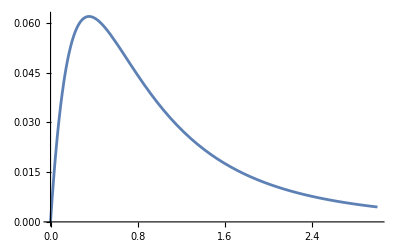

```mathematica
With[{m = 1},Plot[(m^2 r (m+2 r)^2)/(2 (m+r)^7),{r,0,3} ]]
```

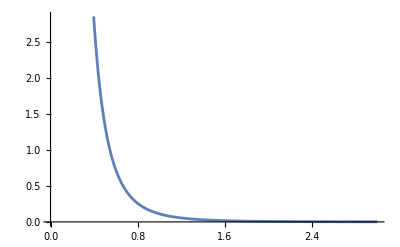

```mathematica
With[{m = 1},Plot[(2 m^3)/(r^2 (m+r) (m+2 r)^2),{r,0,3} ]]
```

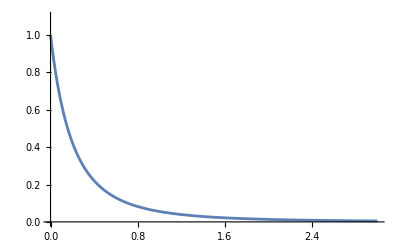

```mathematica
With[{m = 1},Plot[m^3/((m+r) (m+2 r)^2),{r,0,3}, PlotRange->{0,1.1} ]]
```

```mathematica
pointMassEinsteinTensor["Properties"]
```

pointMassEinsteinTensor[Properties]

```mathematica
pointMassEinsteinTensorXYZT["ReducedTrace"]
```

(m^2 (m^2-4 (x^2+y^2+z^2)) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))/(4 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^6)

```mathematica
pointMassEinsteinTensorXYZT["CurvatureSingularities"]
```

{{x→0,y→0,z→0},{z→-√(m^2-x^2-y^2)},{z→√(m^2-x^2-y^2)},{z→-1/2 √(m^2-4 x^2-4 y^2)},{z→1/2 √(m^2-4 x^2-4 y^2)}}

```mathematica
pointMassEinsteinTensorXYZT["RiemannianConditions"]
```

{(m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2>0,(x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^2<0}

```mathematica
pointMassEinsteinTensorXYZT["LorentzianConditions"]
```

{(m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2>0,(x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^2>0}

```mathematica
pointMassEinsteinTensorXYZT["ReducedDeterminant"]
```

(m^11 (m^2+x^2+y^2+z^2+2 m √(x^2+y^2+z^2)))/((x^2+y^2+z^2)^(5/2) (m+√(x^2+y^2+z^2))^12 (m+2 √(x^2+y^2+z^2))^4)

## Ricci Tensor

```mathematica
pointMassRicciTensor= ResourceFunction["RicciTensor"][pointMassMetricXYZT]
```

RicciTensor[…]

```mathematica
pointMassRicciTensor["ReducedMatrixRepresentation"] //MatrixForm
```

((m^2 (m+2 √(x^2+y^2+z^2))^3)/(8 (m+√(x^2+y^2+z^2))^7) | 0 | 0 | 0
0 | (m^2 (4 x^4+4 x^2 (2 y^2+2 z^2+m √(x^2+y^2+z^2))+(y^2+z^2) (-m^2+4 (y^2+z^2)+3 m √(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)
0 | (m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^2 (-m^2 (x^2+z^2)+4 (x^2+y^2+z^2)^2+m √(x^2+y^2+z^2) (3 x^2+4 y^2+3 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)
0 | (m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2) | (m^2 (-m^2 (x^2+y^2)+4 (x^2+y^2+z^2)^2+m √(x^2+y^2+z^2) (3 (x^2+y^2)+4 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2))

```mathematica
FunctionRepository`$74c0beac92b4432eb4ef8a017769f239`RicciTensor[pointMassMetricXYZT]["ReducedMatrixRepresentation"]
```

{{(m^2 (m+2 √(x^2+y^2+z^2))^3)/(8 (m+√(x^2+y^2+z^2))^7),0,0,0},{0,(m^2 (4 x^4+4 x^2 (2 y^2+2 z^2+m √(x^2+y^2+z^2))+(y^2+z^2) (-m^2+4 (y^2+z^2)+3 m √(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2),(m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)},{0,(m^3 x y)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2),(m^2 (-m^2 (x^2+z^2)+4 (x^2+y^2+z^2)^2+m √(x^2+y^2+z^2) (3 x^2+4 y^2+3 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2)},{0,(m^3 x z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2),(m^3 y z)/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))^2),(m^2 (-m^2 (x^2+y^2)+4 (x^2+y^2+z^2)^2+m √(x^2+y^2+z^2) (3 (x^2+y^2)+4 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)}}

```mathematica
pointMassRicciTensor["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,SymbolicMatrixRepresentation,RicciScalar,ReducedRicciScalar,SymbolicRicciScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RicciFlatQ,VanishingRicciScalarQ,RicciFlatConditions,VanishingRicciScalarCondition,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,ScalarCurvatureSingularities,Determinant,ReducedDeterminant,SymbolicDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantRicciTensor,ContravariantRicciTensor,ScalarVolumeExpansion,ReducedScalarVolumeExpansion,SymbolicScalarVolumeExpansion,VolumeFormExpansion,ReducedVolumeFormExpansion,SymbolicVolumeFormExpansion,Properties}

```mathematica
FunctionRepository`$74c0beac92b4432eb4ef8a017769f239`RicciTensor[pointMassMetricXYZT]["Properties"]
```

{MatrixRepresentation,ReducedMatrixRepresentation,SymbolicMatrixRepresentation,RicciScalar,ReducedRicciScalar,SymbolicRicciScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RicciFlatQ,VanishingRicciScalarQ,RicciFlatConditions,VanishingRicciScalarCondition,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,SymmetricQ,DiagonalQ,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,ScalarCurvatureSingularities,Determinant,ReducedDeterminant,SymbolicDeterminant,Eigenvalues,ReducedEigenvalues,Eigenvectors,ReducedEigenvectors,CovariantRicciTensor,ContravariantRicciTensor,ScalarVolumeExpansion,ReducedScalarVolumeExpansion,SymbolicScalarVolumeExpansion,VolumeFormExpansion,ReducedVolumeFormExpansion,SymbolicVolumeFormExpansion,Properties}

```mathematica
pointMassRicciTensor["ReducedRicciScalar"]
```

(m^2 (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)) (-m^2+4 (x^2+y^2+z^2)))/(4 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^6)

```mathematica
FunctionRepository`$74c0beac92b4432eb4ef8a017769f239`RicciTensor[pointMassMetricXYZT]["ReducedRicciScalar"]
```

(m^2 (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)) (-m^2+4 (x^2+y^2+z^2)))/(4 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^6)

## RiemannTensor

```mathematica
pointMassRiemennianTensor= ResourceFunction["RiemannTensor"][pointMassMetricXYZT]
```

RiemannTensor[…]

```mathematica
FunctionRepository`$c392ceb0ded1413a83fcba14e8d68073`RiemannTensor[pointMassMetricXYZT]
```

RiemannTensor[…]

```mathematica
pointMassRiemennianTensor["ReducedTensorRepresentation"]  // MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (m (4 x^4+2 x^2 (y^2+z^2)-(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | (m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | (m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))
(m (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
-(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
-(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0) | (0 | (m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | -(m (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | (m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))
-(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
(m (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
-(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0) | (0 | (m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | (m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | -(m (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))
-(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
-(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0
(m (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))) | 0 | 0 | 0)
(0 | -(m (m+2 √(x^2+y^2+z^2))^3 (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | (m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | (m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)
(m (m+2 √(x^2+y^2+z^2))^3 (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
-(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
-(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | (2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | -(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | -(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0)
(0 | (m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | -(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | (m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)
-(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
-(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | -(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | (2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0)
(0 | (m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | (m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | -(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)
-(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
-(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0
(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | (2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | -(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | -(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | (2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0 | -(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)
0 | -(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | (2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
FunctionRepository`$c392ceb0ded1413a83fcba14e8d68073`RiemannTensor[pointMassMetricXYZT]["ReducedTensorRepresentation"]
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,(m (4 x^4+2 x^2 (y^2+z^2)-(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))},{(m (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{-(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{-(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0}},{{0,(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),-(m (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))},{-(m x y (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{(m (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{-(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0}},{{0,(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),-(m (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2)))},{-(m x z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{-(m y z (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0},{(m (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))),0,0,0}}},{{{0,-(m (m+2 √(x^2+y^2+z^2))^3 (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)},{(m (m+2 √(x^2+y^2+z^2))^3 (-4 x^4-2 x^2 (y^2+z^2)+(y^2+z^2) (2 (y^2+z^2)+m (m+√(x^2+y^2+z^2)))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{-(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{-(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}},{{0,0,0,0},{0,0,-(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,-(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}}},{{{0,(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),-(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)},{-(m x y (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+z^2)+m (x^2+z^2) √(x^2+y^2+z^2)+2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{-(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0}},{{0,0,0,0},{0,0,-(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m (4 m z^2 (x^2+y^2+z^2)-2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+y^2+2 z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,-(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}}},{{{0,(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),-(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8)},{-(m x z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{-(m y z (m+2 √(x^2+y^2+z^2))^3 (6 (x^2+y^2+z^2)+m (m+√(x^2+y^2+z^2))))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0},{(m (m+2 √(x^2+y^2+z^2))^3 (m^2 (x^2+y^2)+m (x^2+y^2) √(x^2+y^2+z^2)+2 (x^2+y^2-2 z^2) (x^2+y^2+z^2)))/(16 (x^2+y^2+z^2) (m+√(x^2+y^2+z^2))^8),0,0,0}},{{0,0,0,0},{0,0,(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m y z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m (4 m y^2 (x^2+y^2+z^2)-2 (x^2-2 y^2+z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (x^2+2 y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),-(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}},{{0,0,0,0},{0,0,-(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,(2 m x z (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0,-(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2)},{0,-(2 m x y (m^2+4 m √(x^2+y^2+z^2)+6 (x^2+y^2+z^2)))/((x^2+y^2+z^2)^(3/2) (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),(2 m (4 m x^2 (x^2+y^2+z^2)+2 (2 x^2-y^2-z^2) (x^2+y^2+z^2)^(3/2)+m^2 √(x^2+y^2+z^2) (2 x^2+y^2+z^2)))/((x^2+y^2+z^2)^2 (m+√(x^2+y^2+z^2))^2 (m+2 √(x^2+y^2+z^2))^2),0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

```mathematica
pointMassRiemennianTensor["Properties"]
```

{TensorRepresentation,ReducedTensorRepresentation,SymbolicTensorRepresentation,KretschmannScalar,ReducedKretschmannScalar,SymbolicKretschmannScalar,ChernPontryaginScalar,ReducedChernPontryaginScalar,SymbolicChernPontryaginScalar,EulerScalar,ReducedEulerScalar,SymbolicEulerScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RiemannFlatQ,VanishingKretschmannScalarQ,VanishingChernPontryaginScalarQ,VanishingEulerScalarQ,RiemannFlatConditions,VanishingKretschmannScalarCondition,VanishingChernPontryaginScalarCondition,VanishingEulerScalarCondition,IndexContractions,ReducedIndexContractions,SymbolicIndexContractions,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,KretschmannSingularities,ChernPontryaginSingularities,EulerSingularities,CovariantRiemannTensor,ContravariantRiemannTensor,Properties}

```mathematica
FunctionRepository`$c392ceb0ded1413a83fcba14e8d68073`RiemannTensor[pointMassMetricXYZT]["Properties"]
```

{TensorRepresentation,ReducedTensorRepresentation,SymbolicTensorRepresentation,KretschmannScalar,ReducedKretschmannScalar,SymbolicKretschmannScalar,ChernPontryaginScalar,ReducedChernPontryaginScalar,SymbolicChernPontryaginScalar,EulerScalar,ReducedEulerScalar,SymbolicEulerScalar,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,RiemannFlatQ,VanishingKretschmannScalarQ,VanishingChernPontryaginScalarQ,VanishingEulerScalarQ,RiemannFlatConditions,VanishingKretschmannScalarCondition,VanishingChernPontryaginScalarCondition,VanishingEulerScalarCondition,IndexContractions,ReducedIndexContractions,SymbolicIndexContractions,CovariantDerivatives,ReducedCovariantDerivatives,SymbolicCovariantDerivatives,BianchiIdentities,SymbolicBianchiIdentities,Dimensions,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,CurvatureSingularities,KretschmannSingularities,ChernPontryaginSingularities,EulerSingularities,CovariantRiemannTensor,ContravariantRiemannTensor,Properties}

```mathematica
(*pointMassRiemennianTensor["ReducedKretschmannScalar"]*)
```

```mathematica
(*pointMassRiemennianTensor["ReducedEulerScalar"]*)
```

```mathematica
(*pointMassRiemennianTensor["CurvatureSingularities"]*)
```

```mathematica
(*pointMassRiemennianTensor["ReducedChernPontryaginScalar"]*)
```

## ChristoffelSymbols

I want to calculate the einstein energy psuedo energy tensor.

```mathematica
"ChristoffelSymbols"
```

ChristoffelSymbols

```mathematica
chrisXYZT = ResourceFunction["ChristoffelSymbols"][pointMassMetricXYZT]
```

ChristoffelSymbols[…]

```mathematica
chrisXYZT["Properties"]
```

{TensorRepresentation,ReducedTensorRepresentation,SymbolicTensorRepresentation,MetricTensor,Coordinates,CoordinateOneForms,Indices,CovariantQ,ContravariantQ,MixedQ,Symbol,VanishingChristoffelQ,VanishingChristoffelConditions,IndexContractions,ReducedIndexContractions,SymbolicIndexContractions,Dimensions,Signature,RiemannianQ,PseudoRiemannianQ,LorentzianQ,RiemannianConditions,PseudoRiemannianConditions,LorentzianConditions,ConnectionSingularities,CovariantChristoffelSymbols,ContravariantChristoffelSymbols,Properties}

```mathematica
chrisXYZT["ReducedTensorRepresentation"] //MatrixForm
```

((0
(m x)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))
(m y)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))
(m z)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))) | ((m x)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))
0
0
0) | ((m y)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))
0
0
0) | ((m z)/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)))
0
0
0)
((m x (m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^7)
0
0
0) | (0
-(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))) | (0
-(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
0) | (0
-(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
0
(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2))))
((m y (m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^7)
0
0
0) | (0
(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
0) | (0
-(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))) | (0
0
-(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2))))
((m z (m+2 √(x^2+y^2+z^2))^4)/(16 (m+√(x^2+y^2+z^2))^7)
0
0
0) | (0
(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
0
-(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))) | (0
0
(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))) | (0
-(2 m x)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m y)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))
-(2 m z)/(√(x^2+y^2+z^2) (m^2+3 m √(x^2+y^2+z^2)+2 (x^2+y^2+z^2)))))

```mathematica
chrisXYZT["ReducedIndexContractions"]
```

<|Γ_σν^σ→{0,(m x (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))),(m y (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))),(m z (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2)))},Γ_μσ^σ→{0,(m x (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))),(m y (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2))),(m z (m-4 √(x^2+y^2+z^2)))/((x^2+y^2+z^2) (m+√(x^2+y^2+z^2)) (m+2 √(x^2+y^2+z^2)))}|>